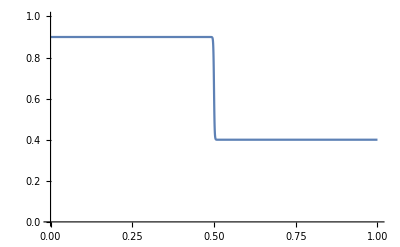

```mathematica
omega = omega0+(omega1-omega0)/(1 + Exp[-1000*(G - mid)])/.{omega0->0.9,omega1->0.4,mid->0.5};
Plot[omega,{G,0,1},PlotRange->{0,1}]
```

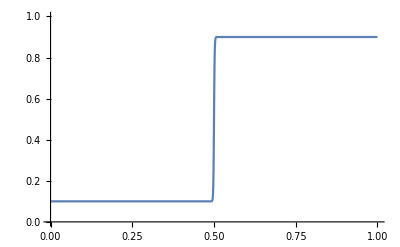

```mathematica
phi = phi0+(phi1-phi0)/(1 + Exp[-1000*(G - mid)])/.{phi0->0.1,phi1->0.9,mid->0.5};
Plot[phi,{G,0,1},PlotRange->{0,1}]
```